# Problem Set 7

## Chapter 18

```mathematica
GeoDistance[,]
```

3453.71 mi

```mathematica
GeoDistance[,]/GeoDistance[,]
```

1.35109

```mathematica
UnitConvert[GeoDistance[,],]
```

14387. km

```mathematica
GeoGraphics[]
```

-Graphics-

```mathematica
GeoListPlot[{,,,}]
```

-Graphics-

```mathematica
GeoGraphics[GeoPath[{,}]]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[,]]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[,GeoDistance[,]]]
```

-Graphics-

```mathematica
GeoImage[GeoDisk[,]]
```

-Graphics-

```mathematica
GeoNearest["Country",GeoPosition["NorthPole" ],5]
```

```mathematica
{Entity["Country","Greenland"],Entity["Country","Canada"],Entity["Country","Russia"],Entity["Country","Svalbard"],Entity["Country","UnitedStates"]}
```


{-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[GeoNearest["Country",GeoPosition[{45,0}],3],"Flag"]
```

```mathematica
GeoListPlot[GeoNearest["Volcano",GeoPosition[Entity["City",{"Rome","Lazio","Italy"}]],25]]
```

-Graphics-

```mathematica
EntityValue[,"Latitude"]-EntityValue[,"Latitude"]
```

6.64488 °

## Chapter 19

```mathematica
UnitConvert[Now-,Quantity[, "Days"]]
```

45696. days

```mathematica
DayName[]
```

Saturday

```mathematica
Now-
```

Wed 28 Apr 1751 21:39:16GMT-7

```mathematica
LocalTime[]
```

Tue 11 Feb 2025 10:10:17GMT+5.5

```mathematica
Sunset[Here,Today]-Sunrise[Here,Today]
```

10.7741 h

```mathematica
MoonPhase[Now,"Icon"]
```

-Graphics-

```mathematica
Table[MoonPhase[n],{n,DayRange[Today,]}]
```

{0.943238,0.981443,0.998399,0.994506,0.971049,0.929957,0.87353,0.804225,0.7245,0.636771}

```mathematica
Table[MoonPhase[n,"Icon"],{n,DayRange[Tomorrow,]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Sunrise[,Today]-Sunrise[,Today]
```

-4.53767 h

```mathematica
UnitConvert[Now-DateObject[],]
```

55.601 yr

```mathematica
AirTemperatureData[,]
```

42.8 °F

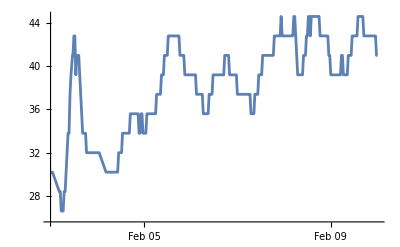

```mathematica
ListLinePlot[AirTemperatureData[,{,Today}]]
```

```mathematica
AirTemperatureData[,Now]-AirTemperatureData[,Now]
```

24. _Δ^◦F

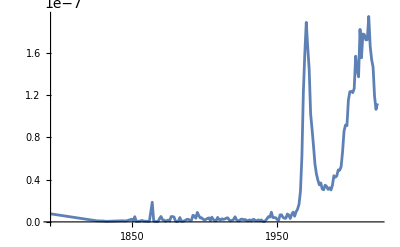

```mathematica
ListLinePlot[WordFrequencyData["groovy","TimeSeries"]]
```

```mathematica
[Dated["Population",2000]]-[Dated["Population",1900]]
```

945542 people